The EIT model

The following Eq. is Eq. (49) of TeX\AtomicPhysics\EIT\Fleischhauer\with noise

```mathematica
χ=χ0 γ31 ⅈ(Ωc^2/(γ21+2ⅈ δ)+(γ31+2ⅈ Δ1))^-1//.{δ->Δ1-Δ2,Δ1->-Δp,Δ2->-Δc}
Reχ[Δp_]:=Evaluate[Re[χ]]/.χ0->1;
Imχ[Δp_]:=Evaluate[Im[χ]]/.χ0->1;
```

(ⅈ γ31 χ0)/(γ31-2 ⅈ Δp+Ωc^2/(γ21+2 ⅈ (Δc-Δp)))

Incoming pulse

```mathematica
TheInt=1/(2π)Integrate[Exp[ⅈ (Δp-Δc) t],{t,-L,L}]
Gauss=Exp[-(Δp-Δc)^2/(2 σ^2)];
Einω=TheInt*Gauss
EinΔ[Δp_]:=Evaluate [Einω];
```

Sin[L (Δc-Δp)]/(π (Δc-Δp))

(ⅇ^(-(-Δc+Δp)^2/(2 σ^2)) Sin[L (Δc-Δp)])/(π (Δc-Δp))

Outgoing pulse

```mathematica
MyRep={ODmax->30,γ31->1.,L->25,γ21->0,Δc->2,Ωc->2,σ->1.};
```

```mathematica
Eoutω=Einω*Exp[ⅈ ODmax/(2χ0)χ]
```

(ⅇ^(-(-Δc+Δp)^2/(2 σ^2)-(ODmax γ31)/(2 (γ31-2 ⅈ Δp+Ωc^2/(γ21+2 ⅈ (Δc-Δp))))) Sin[L (Δc-Δp)])/(π (Δc-Δp))

```mathematica
(*Plot[{Reχ[Δp]/.MyRep,Imχ[Δp]/.MyRep,1/8 EinΔ[Δp]/.MyRep},{Δp,-2,4}]*)
```

```mathematica
Nan[x_] := If[NumericQ[x], x, "nan"];
SetAttributes[Nan, Listable];
SpecTab=Table[{Δp,Reχ[Δp]/.MyRep,Imχ[Δp]/.MyRep,1/8 EinΔ[Δp]/.MyRep},{Δp,-2,4,6/301}];
Export["D:/Temp/Spectrum.txt",SetPrecision[Nan[SpecTab],6],"Table"]
```

D:/Temp/Spectrum.txt

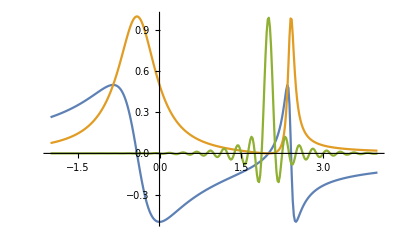

```mathematica
SpecTabRe=Part[SpecTab,All,{1,2}];
SpecTabIm=Part[SpecTab,All,{1,3}];
SpecTabIncom=Part[SpecTab,All,{1,4}];
ListLinePlot[{SpecTabRe,SpecTabIm,SpecTabIncom}]
```

```mathematica
Ein[t_]:=NIntegrate[Einω*Exp[-ⅈ (Δp-Δc) t]/.MyRep,{Δp,-∞,∞}]
```

```mathematica
(*Plot[Abs[Ein[t]]^2,{t,-30,40},PlotRange->All]
Plot[Arg[Ein[t]],{t,-30,40},PlotRange->{Automatic,{-π, π}}]*)
```

```mathematica
Eout[t_]:=NIntegrate[Eoutω*Exp[-ⅈ (Δp-Δc) t]/.MyRep,{Δp,-∞,∞}]
```

```mathematica
Timing[ExpTab=Table[{t,Abs[Ein[t]]^2,Abs[Eout[t]]^2,Arg[Eout[t]]},{t,-30,40,70/401}];]
Export["D:/Temp/TimeDomain.txt",SetPrecision[Nan[ExpTab],6],"Table"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Δp near {Δp} = {1.99415}. NIntegrate obtained -0.000151701 - 0.000242592\ ⅈ and 0.022761 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Δp near {Δp} = {1.99415}. NIntegrate obtained -0.000151732 - 0.000243233\ ⅈ and 0.022757 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{95.8938,Null}

D:/Temp/TimeDomain.txt

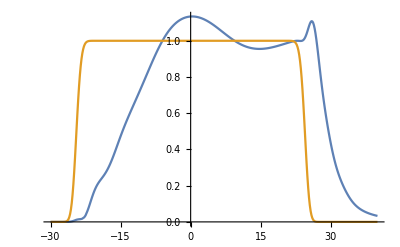

```mathematica
AbsTabIn=Part[ExpTab,All,{1,2}];
AbsTabOut=Part[ExpTab,All,{1,3}];
ListLinePlot[{AbsTabOut,AbsTabIn}]
```

```mathematica
(*Timing[ExpTabArg=Table[{t,Arg[Eout[t]]},{t,-30,40,70/401}];]
Export["D:/Temp/Arg.txt",SetPrecision[Nan[ExpTabArg],6],"Table"]*)
```

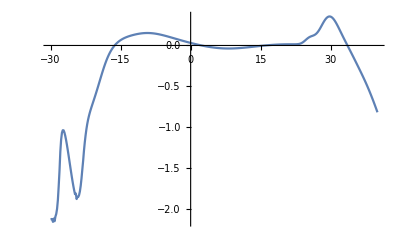

```mathematica
ArgTab=Part[ExpTab,All,{1,4}];
ListLinePlot[ArgTab,PlotRange->All]
```

```mathematica
(*Plot[Abs[Eout[t]]^2,{t,-25,35}]*)
(*Plot[Arg[Eout[t]],{t,-25,35},PlotRange->All]*)
```